# Radau & Lobatto Polynomials

## coded by Manuel Diaz, NTU, 2013.08.21

Following Ideas in Polynomials Review found in:
1. A Flux Reconstruction Approach to High-Order Schemes Including Discontinuous
Galerkin Methods. H. T. Huynh. AIAA Conference Paper, 2007-4079, 2007

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

#### Change Notebook BackGround

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]] (* type of gray *)
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]] (* Pastel Green *)
```

#### Set back to original colors

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]] (* white *)
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0/255,0/255,0/255]] (* Black *)
```

### Initialize Notation

```mathematica
Needs["Notation`"]
```

based on http://en.wikipedia.org/wiki/Gram-Schmidt_process, we configure:

```mathematica
Notation[<a_,b_> ⟹ Integrate[a_ b_,{x,-1,1}]]
```

```mathematica
Notation[Subscript[proj, u_][v_] ⟹ (<u_,v_>)/(<u_,u_>)u_]
```

Testing:

```mathematica
<Subscript[v, 1][z],Subscript[v, 1][z]>
```

2 v_1[z]^2

```mathematica
<a z,z>
```

2 a z^2

```mathematica
(<a[z],b[z]>)/(<a[z],a[z]>)a[z] == Subscript[proj, a[z]][b[z]]
```

True

```mathematica
Symbolize[Subscript[Δx, j]]; Symbolize[Subscript[x, j]];Symbolize[Subscript[I, j]];
```

## A. The Legendre Polynomials

Generating up to 4th degree.

```mathematica
legendreP = Table[LegendreP[i,x],{i,0,5}];
```

```mathematica
Table[Subscript[p, i]= legendreP[[i+1]],{i,0,5}];
{Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5]}
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5)}

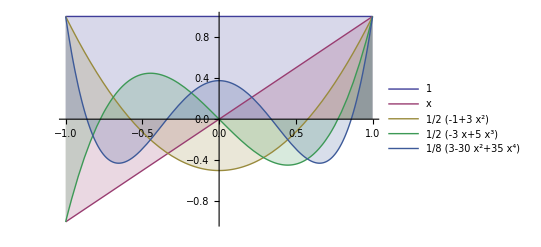

```mathematica
Plot[Evaluate[Most[legendreP]],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[(<Subscript[p, i],Subscript[p, j]>),{i,0,4},{j,0,4}] //TableForm
```

2 | 0 | 0 | 0 | 0
0 | 2/3 | 0 | 0 | 0
0 | 0 | 2/5 | 0 | 0
0 | 0 | 0 | 2/7 | 0
0 | 0 | 0 | 0 | 2/9

## B. Radau Polynomials

Left Radau Polynomials (“is zero at the left side”)

```mathematica
Subscript[Radau, left]= Table[1/2(Subscript[p, k]+Subscript[p, k-1]),{k,1,4}]//Expand//Simplify;
```

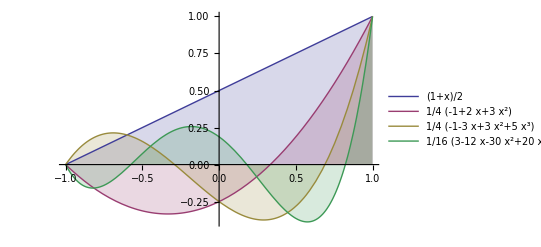

```mathematica
Plot[Evaluate[Subscript[Radau, left]],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[R, L,i]= Subscript[Radau, left][[i]],{i,1,4}];
```

```mathematica
Table[(<Subscript[R, L,i],Subscript[R, L,j]>),{i,1,4},{j,1,4}] //TableForm
```

2/3 | 1/6 | 0 | 0
1/6 | 4/15 | 1/10 | 0
0 | 1/10 | 6/35 | 1/14
0 | 0 | 1/14 | 8/63

Right Radau Polynomials (“zero at the right side”)

```mathematica
Subscript[Radau, right]= Table[(-1)^k/2(Subscript[p, k]-Subscript[p, k-1]),{k,1,4}]//Simplify;
```

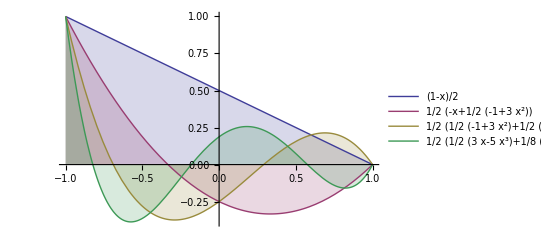

```mathematica
Plot[Evaluate[Subscript[Radau, right]],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[R, R,i]= Subscript[Radau, right][[i]],{i,1,4}];
```

```mathematica
Table[(<Subscript[R, R,i],Subscript[R, R,j]>),{i,1,4},{j,1,4}] //TableForm
```

2/3 | 1/6 | 0 | 0
1/6 | 4/15 | 1/10 | 0
0 | 1/10 | 6/35 | 1/14
0 | 0 | 1/14 | 8/63

## C. Lobatto Polynomials

Lobatto Polynomials (by Legendre Polynomials)

```mathematica
lobatto = Table[Subscript[p, k]-Subscript[p, k-2],{k,2,5}] //Simplify;
```

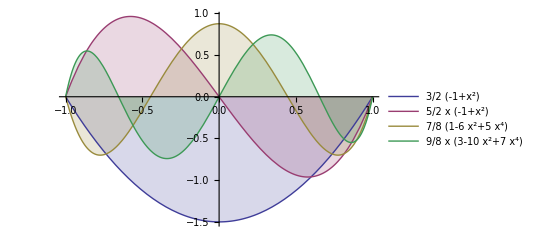

```mathematica
Plot[Evaluate[lobatto],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[Lo, i]= lobatto[[i]],{i,1,4}]//TableForm
```

3/2 (-1+x^2)
5/2 x (-1+x^2)
7/8 (1-6 x^2+5 x^4)
9/8 x (3-10 x^2+7 x^4)

```mathematica
Table[(<Subscript[Lo, i],Subscript[Lo, j]>),{i,1,4},{j,1,4}] //TableForm
```

12/5 | 0 | -2/5 | 0
0 | 20/21 | 0 | -2/7
-2/5 | 0 | 28/45 | 0
0 | -2/7 | 0 | 36/77

Roots of a lobatto Polynomial of order i,

```mathematica
lobattoRoots = List@@Roots[Evaluate[Subscript[Lo, 3]]==0,x][[All,2]]
```

{1/(√5),-1/(√5),-1,1}

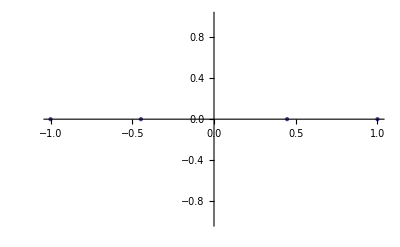

```mathematica
lobattoPoints = ListPlot[Table[{lobattoRoots[[i]],0},{i,1,4}],PlotStyle->PointSize[Large]]
```

Lobatto Polynomials (by Radau Polynomials)

```mathematica
lobatto2 = Table[2(Subscript[R, L,k]-Subscript[R, L,k-1]),{k,2,5}]//Simplify;
```

-Graphics-

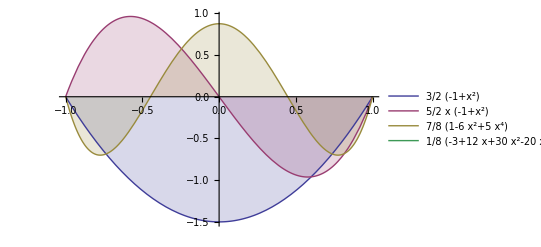

```mathematica
Plot[Evaluate[lobatto2],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

## D. Weighted average of the Radau Polynomials

Lumped Radau Polynomials to match the lobatto roots.

```mathematica
Subscript[weigthedRadau, left] = Table[(k-1)/(2k-1)Subscript[R, L,k]+ k/(2k-1)Subscript[R, L,k-1],{k,2,4}];
```

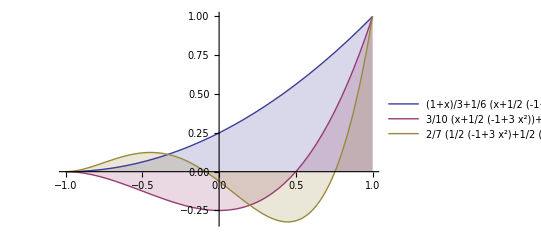

```mathematica
Plot[Evaluate[Subscript[weigthedRadau, left]],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[R, L,wa,i]=Subscript[weigthedRadau, left][[i-1]],{i,2,4}];
```

```mathematica
Table[(<Subscript[R, L,wa,i],Subscript[R, L,wa,j]>),{i,2,4},{j,2,4}] //TableForm
```

2/5 | 2/15 | 2/105
2/15 | 6/35 | 3/35
2/105 | 3/35 | 4/35

```mathematica
Subscript[weigthedRadau, right] = Table[(k-1)/(2k-1)Subscript[R, R,k]+ k/(2k-1)Subscript[R, R,k-1],{k,2,4}];
```

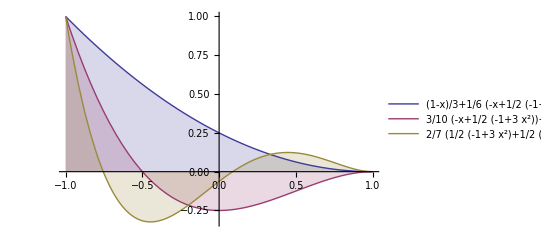

```mathematica
Plot[Evaluate[Subscript[weigthedRadau, right]],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[R, R,wa,i]=Subscript[weigthedRadau, right][[i-1]],{i,2,4}];
```

```mathematica
Table[(<Subscript[R, R,wa,i],Subscript[R, R,wa,j]>),{i,2,4},{j,2,4}] //TableForm
```

2/5 | 2/15 | 2/105
2/15 | 6/35 | 3/35
2/105 | 3/35 | 4/35

## Ploting the Lumped polynomail over Lobatto roots.

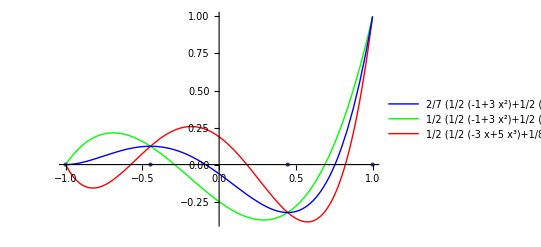

```mathematica
Show[
Plot[Evaluate[Subscript[R, L,4]],{x,-1,1},PlotStyle -> {Red},PlotLegends->"Expressions"],
Plot[Evaluate[Subscript[R, L,3]],{x,-1,1},PlotStyle -> {Green},PlotLegends->"Expressions"],
Plot[Evaluate[Subscript[R, L,wa,4]],{x,-1,1},PlotStyle -> {Blue},PlotLegends->"Expressions"],
lobattoPoints]
```